# Characterization of localized bulging using the 1D model of Yu and Fu (2022)

This Mathematica code  produces some of the figures presented in Yu and Fu (2022)

```mathematica
Clear["`*"]
```

## 1. Symbolic Calculations

### (I). Define the strain energy function and related quantities

```mathematica
W[x_,y_,z_]=-1/2 Jm Log[1-(x^2+y^2+z^2-3)/Jm]/.{Jm->97.2}; 
w[x_,y_]=W[x,y,x^-1 y^-1]; 
W1[x_,y_,z_]=D[W[x,y,z],x];
W2[x_,y_,z_]=D[W[x,y,z],y];
W3[x_,y_,z_]=D[W[x,y,z],z];
w1[x_,y_]=D[w[x,y],x];
w2[x_,y_]=D[w[x,y],y];
ζt[x_,y_]=(y w2[x,y])/(y^2-(x^-1 y^-1)^2); (*this is the ζ in (4.9) *)
```

### (II). Define the two functions Q[a,λ] and M[a,λ]

```mathematica
(*Q[a,λ]:=(∫__b)^a w1[λ1,λ]/(λ1^2 λ-1)dλ1 and M[a,λ]:=(∫_b)^a((λ1^2-a^2)w1[λ1,λ]+2λ1λ(a^2 λ-1)w2[λ1,λ])/(2 (λ1^2 λ-1)^2)dλ1; see (3.6) and (3.9)*)
```

```mathematica
Qint=Integrate[w1[λ1,λ]/(λ1^2 λ-1),λ1];    (*the integrand in (3.6) *)
b=(√(a^2 A^2+λ^-1(B^2-A^2)))/B;      (*azimuthal stretch at R= B *)
Q[a_,λ_]=(Qint/.λ1->a)-(Qint/.λ1->b); 
Mint=Integrate[((λ1^2-a^2)w1[λ1,λ]+2λ1 λ  (a^2 λ-1)w2[λ1,λ])/(2(λ1^2 λ-1)^2),λ1];
M[a_,λ_]=(Mint/.λ1->a)-(Mint/.λ1->b);
F[a_,λ_]=M[a,λ]-1/2 a^2 Q[a,λ]; (* resulant axial force scaled by 2 πA^2*)
Ω[a_,λ_]=Derivative[1,0][Q][a,λ]Derivative[0,1][F][a,λ] -Derivative[0,1][Q][a,λ] Derivative[1,0][F][a,λ] (*Ω[a,λ]=0 is the bifurcation condition*);
```

### (III). Define the two functions q[λ1, λ] and m[λ1, λ], and the functions G[a ,λ] and λ'[a]

```mathematica
qint=Integrate[w1[λ1til,λ]/(λ1til^2 λ-1),λ1til];  (*see eqn (3.13) *)
qt[λ1_,λ_]=(qint/.λ1til->λ1)-(qint/.λ1til->b) (* q[a,R]= qt[λ1[a,R],λ[a]]; see sect 4 below *);
mint=Integrate[((λ1til^2-λ1^2)w1[λ1til,λ]+2λ1til λ(λ1^2 λ-1)   w2[λ1til,λ])/(2(λ1til^2 λ-1)^2),λ1til];(*see eqn (3.14) *)
mt[λ1_,λ_]=(mint/.λ1til->λ1)-(mint/.λ1til->b)  (*m[a,R]= mt[λ1[a,R],λ[a]]; see set 4 below *);
Gint= A^2 Integrate[w[λ1,λ] (λ1 λ(a^2 λ-1))/((λ1^2 λ-1)^2),λ1];
G[a_,λ_]=(Gint/.λ1->a)-(Gint/.λ1->b)-1/2 P A^2 a^2 λ- NN/(2π)λ; (*see eqn (3.10) *)
GGint=A^2 Integrate[(2λ1(λ a^2-1)(w[λ1,λ]- λ  w2[λ1,λ])-(λ1^2-a^2)w1[λ1,λ])/(2 (λ1^2 λ -1)^2)λ,λ1];
GG[a_,λ_]=(GGint/.{λ1->a})-(GGint/.{λ1->b});(* a simplified form of G[a,λ]*)
eq[a_,λ_]=M[a,λ]-1/2 P a^2 -NN/(2 π A^2); (*implicit equation satisified by λ[a]*)
λp[a_,λ_]=-(Derivative[1,0][eq][a,λ])/(Derivative[0,1][eq][a,λ]);  (*λ'[a]=dλ[a]/da*)
```

### (IV). Define the gradient modulus D[a]

```mathematica
r[a_,R_]=√(a^2 A^2+λ[a]^-1(R^2-A^2));
λ1[a_,R_]=r[a,R]/R;
ζ[a_,R_]=ζt[λ1[a,R],λ[a]];
q[a_,R_]=qt[λ1[a,R],λ[a]];
m[a_,R_]=mt[λ1[a,R],λ[a]];
c[a_,R_]=- (Derivative[1,0][r][a,R])/(λ1[a,R] λ[a]^2)+1/(R ζ[a,R])(R^2 Derivative[1,0][m][a,R]-r[a,R]Derivative[1,0][r][a,R] q[a,R]); (*see eqn (4.18) *)
y0=2.8;
λλ[a_?NumericQ]:=y/.FindRoot[eq[a,y]==0 ,{y,y0}]; (* λλ[a] denotes λ[a] determined from the implicit equation (3.11)*)
𝔻[a_?NumericQ]:=Module[{λz},λz=y/.FindRoot[eq[a,y]==0 ,{y,y0}];NIntegrate[R ζ[μ,R]((Derivative[1,0][r][μ,R])^2-c[μ,R]^2)/.{λ[μ]->λz, λ'[μ]->λp[a,λz]} /.{μ->a},{R,A,B}]]
Δh=10^-6;
𝔻p[a_?NumericQ]:=(𝔻[a+Δh]-𝔻[a-Δh])/(2 Δh) (*numerical derivative of D[a];  this is optional and is used to speed up calculations*)
```

### (V). Geometric parameters

```mathematica
Rm=1;
H=0.4; {A, B}={Rm-H/2, Rm+H/2};
```

### (VI). Test run

```mathematica
NN=0.1; P=0.2;
test=λλ[1.5]
test={𝔻[1.5],𝔻'[1.5],𝔻p[1.5]}
𝔻'[1.5]-𝔻p[1.5]
Clear[NN, P]
```

1.02743

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0981385,0.0772583,0.0772583}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.11802×10^-8

## 2. Weakly nonlinear analysis

### (I). Weakly nonlinear amplitude equation

```mathematica
(* is given by  𝔻[a∞,λ∞] y''[Z]=ω[a∞,γ∞] y[Z]+γ[a∞,γ∞] y[Z]^2, where a[Z]=a∞+y[Z]. *)
```

```mathematica
ω[a_,λ_]:=(2 a A^2 λ (-Derivative[0,1][Q][a,λ] Derivative[1,0][F][a,λ]+Derivative[0,1][F][a,λ] Derivative[1,0][Q][a,λ]))/(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ]);
γ[a_,λ_]:=1/2 A^2 (2 λ Derivative[1,0][Q][a,λ]+(a (2 Derivative[0,1][Q][a,λ]+λ Derivative[0,2][Q][a,λ]) (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ])^2)/(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ])^2-(2 (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ]) (λ Derivative[0,1][Q][a,λ]+a (Derivative[1,0][Q][a,λ]+λ Derivative[1,1][Q][a,λ])))/(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ])+a λ Derivative[2,0][Q][a,λ]+(a λ Derivative[0,1][Q][a,λ] (-((2 Derivative[0,2][F][a,λ]+a^2 Derivative[0,2][Q][a,λ]) (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ])^2)+2 (2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ]) (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ]) (2 a Derivative[0,1][Q][a,λ]+2 Derivative[1,1][F][a,λ]+a^2 Derivative[1,1][Q][a,λ])-(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ])^2 (4 a Derivative[1,0][Q][a,λ]+2 Derivative[2,0][F][a,λ]+a^2 Derivative[2,0][Q][a,λ])))/(8 (Derivative[0,1][F][a,λ]+1/2 a^2 Derivative[0,1][Q][a,λ])^3));
Γ[a_,λ_]:=Derivative[1,0][Ω][a,λ]Derivative[0,1][F][a,λ] -Derivative[0,1][Ω][a,λ] Derivative[1,0][F][a,λ];
k[a_,λ_]:=-(2 λ)/λp[a,λ] (* y(Z)=k c1[λ Z]*)
ΓΓ[a_,λ_]:=- a A^2(a+ (2 λ)/λp[a,λ]);(* sigifies Γ defined in Ye et al. JMPS 2020*)
rm[a_,λ_]=(a A+√(a^2 A^2+λ^-1(B^2-A^2)))/2;(*deformed average radius*)
```

### (II). Bifurcation condition Ω=0 and the curves corresponding to N=0 and λ∞=1.5

```mathematica
(* The intersections between Ω=0 and N=0 give the bifurcation values when axial force is fixed to be zero
The intersections between Ω=0 and λ=1.5 give the bifurcation values when the tube length is fixed to be 1.5 times its undeformed length
 *)
```

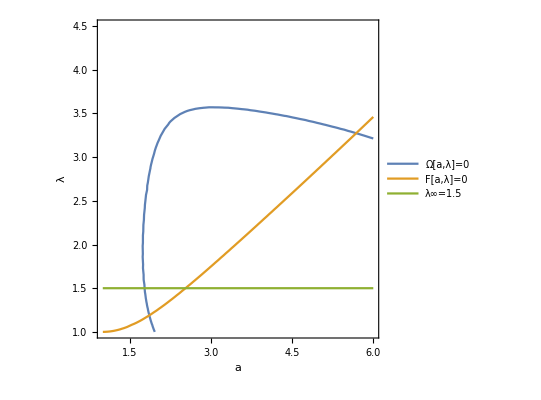

```mathematica
ContourPlot[{Ω[x,y]==0,F[x,y]==0,y==1.5},{x,1,6},{y,1,4.5},FrameLabel->{{HoldForm[λ],None},{HoldForm[a],None}},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[LineLegend[{"Ω[a,λ]=0","F[a,λ]=0","λ∞=1.5"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.5,0.85}]]
```

### (III). Case 1: fixed N=0

```mathematica
{a∞,λ∞}={x,y}/.FindRoot[{ω[x,y]==0,F[x,y]==0},{x,2},{y,1.2}];
P=Q[a∞,λ∞];
NN=2π A^2 F[a∞,λ∞];
(*k1--k4 should be the same as that given in Table 2, Page 10 (Ye et al.JMPS 2020)*)
k1=(Derivative[1,0][ω][a∞,λ∞]+Derivative[0,1][ω][a∞,λ∞]λp[a∞,λ∞])/(𝔻[a∞](λ∞)^2);
k2=(k[a∞,λ∞] γ[a∞,λ∞])/((λ∞)^2 𝔻[a∞]);
k3=k1/(1-H/2)
k4=k2/(rm[a∞,λ∞]+ΓΓ[a∞,λ∞]/rm[a∞,λ∞])
```

-2.81731

-1.5804

Validation of the simplified expressions for ω[a∞,λ∞]  and γ[a∞,λ∞]

```mathematica
ω[a∞,λ∞]-(2 A^2 a∞ λ∞)/(2 Derivative[0,1][F][a∞,λ∞]+(a∞)^2 Derivative[0,1][Q][a∞,λ∞])Ω[a∞,λ∞]//Simplify  (*see eqn (5.24)*)
γ[a∞,λ∞]-(A^2 a∞ λ∞ (2 Derivative[1,0][F][a∞,λ∞]+(a∞)^2 Derivative[1,0][Q][a∞,λ∞]))/((2 Derivative[0,1][F][a∞,λ∞]+(a∞)^2 Derivative[0,1][Q][a∞,λ∞])^2 Derivative[1,0][F][a∞,λ∞])Γ[a∞,λ∞] //Simplify (*see eqn (5.25)*)
```

-2.90968×10^-13

-2.18436×10^-13

### (IV). Case 2: fixed λ∞=1.5

```mathematica
λ∞=1.5;
a∞=x/.FindRoot[ω[x,λ∞]==0,{x,2}];
P=Q[a∞,λ∞];
NN=2π A^2 F[a∞,λ∞];
(*k1--k4 should be the same as that given in Table 1, Page 10 (Ye et al.JMPS 2020)*)
k1=(Derivative[1,0][ω][a∞,λ∞])/(𝔻[a∞](λ∞)^2);
k2=(k[a∞,λ∞]γ[a∞,λ∞])/((λ∞)^2 𝔻[a∞]);
k3=k1/(1-H/2)
k4=k2/(rm[a∞,λ∞]+ΓΓ[a∞,λ∞]/rm[a∞,λ∞])
```

-1.00099

-0.587891

## 3. Case 1 : Fixed N=0

### (I). First bifurcation point

```mathematica
Nc=0;
λN[a_?NumericQ]:=y/.FindRoot[F[a,y]==Nc,{y,y0}];(*used to calculate λ∞*)
{acr,λcr}={x,y}/.FindRoot[{Ω[x,y]==0,F[x,y]==Nc},{x,2},{y,1.2}];
Pcr=Q[acr,λcr];
bifpt={acr,Pcr}
```

{1.85979,0.307892}

### (II). Maxwell state

```mathematica
Clear[a∞,λ∞]
maxwsub=FindRoot[{M[a∞,λ∞]-1/2(a∞)^2 Q[a∞,λ∞]==Nc,M[a0,λ0]-1/2 a0^2 Q[a∞,λ∞]==Nc,GG[a0,λ0]==GG[a∞,λ∞],Q[a0,λ0]==Q[a∞,λ∞]},{{a∞,1.25},{λ∞,1.01},{a0,6.9},{λ0,4}}];
{aM,λM}={a∞,λ∞}/.maxwsub;
PM=Q[aM,λM];
maxwpt={aM,PM}
```

{1.25524,0.196608}

### (III). Collect the {a0,P} and {a∞,a0-∞} data when a∞ decreases from acr

#### 3.1 Near the bifurcation point

```mathematica
dataP={{acr,Pcr}};
dataa0={{acr,0}};
nn=200;
kend=10;
max=20;
Do[a∞=acr-k*(acr-aM)/nn;
λ∞=λN[a∞];
P=Q[a∞,λ∞];
NN=2π A^2(M[a∞,λ∞]-1/2 (a∞)^2 P);
{a0,λ0}={x,y}/.FindRoot[{G[x,y]==G[a∞,λ∞],eq[x,y]==0},{x,1.1acr,acr,max},{y,1.1 λcr,λcr,max}];dataP=Append[dataP,{a0,P}];dataa0=Append[dataa0,{a∞,a0-a∞}],{k,1,kend}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

#### 3.2 Away from the bifurcation point

```mathematica
Do[a∞=acr-k*(acr-aM)/nn;
λ∞=λN[a∞];
P=Q[a∞,λ∞];
NN=2π A^2(M[a∞,λ∞]-1/2 (a∞)^2 P);
{a0,λ0}={x,y}/.FindRoot[{G[x,y]==G[a∞,λ∞],eq[x,y]==0},{x,1.01a0,acr,max},{y,1.01 λ0,λcr,max}];dataP=Append[dataP,{a0,P}];dataa0=Append[dataa0,{a∞,a0-a∞}],{k,kend+1,nn}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
dataPAbaqus={{1.,0.},{1.0700419321656227,0.07009857296943665},{1.124624565243721,0.11524093151092529},{1.1661660820245743,0.1448457717895508},{1.200793981552124,0.16673718690872194},{1.231075331568718,0.18399131298065186},{1.2583262622356415,0.19812821149826051},{1.2833179533481598,0.21001427173614504},{1.3065471649169922,0.22019469738006592},{1.3283537328243256,0.22903497219085694},{1.3489831387996674,0.2367940902709961},{1.3686181902885437,0.24366164207458496},{1.3874000906944275,0.24978158473968506},{1.405440777540207,0.25526616573333744},{1.422829419374466,0.26020350456237795},{1.4396397471427917,0.26466534137725833},{1.4559334218502045,0.26871068477630616},{1.4717613756656647,0.27238771915435794},{1.4871682524681091,0.2757377862930298},{1.5021914839744568,0.27879526615142824},{1.5168641209602356,0.28158996105194095},{1.531214952468872,0.28414733409881593},{1.545269250869751,0.2864896059036255},{1.559049904346466,0.28863623142242434},{1.5725769400596619,0.2906042098999024},{1.585868775844574,0.2924086570739746},{1.5989419221878052,0.2940629005432129},{1.6118113994598389,0.29557883739471436},{1.6244912147521973,0.29696719646453856},{1.6369942426681519,0.2982375144958496},{1.6493326425552368,0.2993984937667847},{1.6615177392959595,0.3004578828811646},{1.6735605597496033,0.30142281055450443},{1.685471534729004,0.30229973793029785},{1.6972612142562866,0.3030945062637329},{1.708940029144287,0.30381250381469727},{1.7205187678337097,0.30445864200592043},{1.732008934020996,0.3050374031066895},{1.7434231638908386,0.3055529356002808},{1.7547759413719177,0.3060090303421021},{1.766084611415863,0.3064091205596924},{1.777371346950531,0.3067564249038697},{1.788666009902954,0.30705382823944094},{1.8000121116638184,0.3073039293289185},{1.8114780187606812,0.30750904083251956},{1.823182761669159,0.3076711177825928},{1.8353612422943115,0.307791543006897},{1.8485665917396545,0.3078706026077271},{1.8645433187484741,0.3079050302505493},{1.8944306373596191,0.30785861015319826},{1.9545928835868835,0.3075614929199219},{2.0011311769485474,0.3071647882461548},{2.04448664188385,0.3066657781600952},{2.087413787841797,0.3060537338256836},{2.131059765815735,0.3053171157836914},{2.1761611700057983,0.3044417142868042},{2.2233389616012573,0.3034098148345947},{2.273219108581543,0.30219919681549073},{2.3265087604522705,0.30078160762786865},{2.3840694427490234,0.2991207122802734},{2.4470064640045166,0.29716875553131106},{2.51679265499115,0.29486191272735596},{2.5954411029815674,0.29211370944976806},{2.6857011318206787,0.28880839347839354},{2.7910492420196533,0.2848047256469727},{2.9144744873046875,0.279994535446167},{3.0541090965270996,0.2744957447052002},{3.1992430686950684,0.2688117742538452},{3.337860345840454,0.2634827852249146},{3.4652140140533447,0.2587149143218994},{3.581627130508423,0.2544872760772705},{3.6887669563293457,0.2507194042205811},{3.7882542610168457,0.24733326435089112},{3.881387948989868,0.24426558017730715},{3.9691667556762695,0.24146692752838136},{4.052355766296387,0.23889868259429933},{4.131548881530762,0.23653032779693606},{4.20721435546875,0.23433735370635989},{4.279726505279541,0.2322997331619263},{4.349390268325806,0.2304009199142456},{4.416457176208496,0.22862699031829836},{4.481137275695801,0.22696616649627688},{4.543608903884888,0.22540826797485353},{4.604024171829224,0.2239445209503174},{4.662514925003052,0.22256720066070557},{4.719196319580078,0.2212695837020874},{4.774169206619263,0.22004563808441163},{4.827523469924927,0.21888999938964845},{4.8793394565582275,0.2177978277206421},{4.929689645767212,0.21676483154296877},{4.978639125823975,0.21578702926635743},{5.026247501373291,0.2148608922958374},{5.072569370269775,0.2139831066131592},{5.117654800415039,0.2131507158279419},{5.161550045013428,0.21236097812652588},{5.204298496246338,0.21161131858825685},{5.245940208435059,0.2108994245529175},{5.28651237487793,0.2102231502532959},{5.326050758361816,0.20958044528961184},{5.364588260650635,0.20896944999694825},{5.402155876159668,0.20838844776153564},{5.438783645629883,0.20783581733703616},{5.4745001792907715,0.20731000900268556},{5.509331226348877,0.2068095922470093},{5.5433030128479,0.20633327960968018},{5.576440334320068,0.205879807472229},{5.608765125274658,0.20544798374176027},{5.64030122756958,0.20503673553466797},{5.671069145202637,0.2046449661254883},{5.701090335845947,0.2042717695236206},{5.73038387298584,0.20391616821289063},{5.758969306945801,0.20357728004455566},{5.786865234375,0.2032543420791626},{5.814089298248291,0.20294651985168458},{5.840659141540527,0.2026530981063843},{5.866590976715088,0.20237338542938232},{5.891901016235352,0.20210669040679932},{5.916604995727539,0.2018524408340454},{5.940718650817871,0.20160996913909912},{5.9642558097839355,0.20137877464294435},{5.987231254577637,0.20115830898284914},{6.0096588134765625,0.20094804763793947},{6.031551837921143,0.20074751377105715},{6.052923202514648,0.20055623054504396},{6.073786735534668,0.20037381649017336},{6.09415340423584,0.20019981861114503},{6.114036560058594,0.20003383159637453},{6.13344669342041,0.19987550973892212},{6.1523966789245605,0.19972448348999025},{6.170896053314209,0.19958041906356813},{6.1889567375183105,0.19944298267364502},{6.206589221954346,0.19931188821792603},{6.223803520202637,0.19918681383132936},{6.240609645843506,0.19906750917434693},{6.257017135620117,0.19895368814468384},{6.273036003112793,0.19884510040283204},{6.288675785064697,0.1987415075302124},{6.3039445877075195,0.19864268302917482},{6.318851947784424,0.19854841232299805},{6.3334059715271,0.198458468914032},{6.347615718841553,0.1983726739883423},{6.361489295959473,0.19829081296920778},{6.375033855438232,0.19821273088455202},{6.388258457183838,0.19813823699951172},{6.401169776916504,0.19806717634201051},{6.413775444030762,0.19799939393997193},{6.426082611083984,0.19793472290039063},{6.438098907470703,0.1978730320930481},{6.449830532073975,0.19781419038772585},{6.461284637451172,0.19775805473327637},{6.472467422485352,0.19770450592041017},{6.483386039733887,0.19765342473983766},{6.494046211242676,0.19760470390319826},{6.504453659057617,0.19755823612213136},{6.514615535736084,0.19751391410827637},{6.5245361328125,0.19747163057327272},{6.534222602844238,0.19743130207061768},{6.543679714202881,0.19739284515380862},{6.552912712097168,0.19735615253448488},{6.561927318572998,0.19732116460800173},{6.570728778839111,0.19728779792785645},{6.579321384429932,0.19725598096847535},{6.587710857391357,0.1972256302833557},{6.595901966094971,0.1971966862678528},{6.603899002075195,0.19716907739639283},{6.611706256866455,0.19714275598526002},{6.61932897567749,0.19711765050888064},{6.626771450042725,0.19709371328353884},{6.634037494659424,0.1970708966255188},{6.6411309242248535,0.19704912900924684},{6.648056983947754,0.19702837467193604},{6.654818534851074,0.1970085859298706},{6.6614203453063965,0.19698971509933472},{6.66786527633667,0.19697172641754152},{6.674157619476318,0.1969545841217041},{6.680300712585449,0.19693822860717775},{6.686298370361328,0.1969226360321045},{6.692153453826904,0.19690777063369752},{6.697870254516602,0.19689360857009888},{6.703451156616211,0.19688010215759277},{6.708899974822998,0.1968672275543213},{6.714219093322754,0.19685494899749756},{6.719412326812744,0.19684325456619264},{6.72448205947876,0.19683209657669068},{6.729431629180908,0.19682146310806276},{6.734263896942139,0.19681133031845094},{6.738981246948242,0.19680167436599733},{6.743586540222168,0.196792471408844},{6.748082637786865,0.19678369760513306},{6.752471923828125,0.19677534103393557},{6.756756782531738,0.1967673659324646},{6.760940074920654,0.19675977230072023},{6.765023708343506,0.1967525362968445},{6.769010066986084,0.1967456340789795},{6.772902011871338,0.19673906564712526},{6.7767014503479,0.19673280715942384},{6.780410289764404,0.19672683477401734},{6.784030914306641,0.19672114849090577},{6.7875657081604,0.19671573638916018},{6.791016101837158,0.19671057462692262},{6.794384479522705,0.19670565128326417},{6.797672271728516,0.19670096635818482},{6.800881862640381,0.19669650793075563},{6.804015159606934,0.19669225215911867},{6.807074069976807,0.1966882109642029},{6.810059547424316,0.19668434858322145},{6.812974452972412,0.19668067693710328},{6.815819263458252,0.1966771721839905},{6.818596363067627,0.19667383432388308},{6.821307182312012,0.19667066335678102},{6.823953628540039,0.19666763544082644},{6.826536655426025,0.1966647505760193},{6.8290581703186035,0.19666200876235962},{6.83151912689209,0.19665939807891847},{6.833921432495117,0.19665690660476687},{6.83626651763916,0.1966545343399048},{6.838555335998535,0.1966522812843323},{6.840789318084717,0.1966501235961914},{6.842970371246338,0.1966480851173401},{6.845098495483398,0.19664613008499146},{6.847176551818848,0.19664427042007449},{6.849204063415527,0.19664250612258913},{6.8511834144592285,0.19664082527160645},{6.853115558624268,0.19663922786712648},{6.855000972747803,0.19663770198822023},{6.856841564178467,0.1966362476348877},{6.858637809753418,0.1966348648071289},{6.860390663146973,0.19663355350494385},{6.862102031707764,0.19663230180740357},{6.863771915435791,0.19663110971450806},{6.8654022216796875,0.19662997722625733},{6.866992950439453,0.19662889242172243},{6.8685455322265625,0.1966278672218323},{6.870060920715332,0.19662688970565798},{6.87153959274292,0.19662595987319947},{6.872982978820801,0.1966250777244568},{6.874391555786133,0.196624231338501},{6.875766277313232,0.196623432636261},{6.877107620239258,0.19662266969680786},{6.878417015075684,0.19662194252014162},{6.87969446182251,0.19662125110626222},{6.880941390991211,0.1966205954551697},{6.882158279418945,0.19661997556686403},{6.883346080780029,0.19661937952041628},{6.884504795074463,0.1966188192367554},{6.885635852813721,0.19661828279495241},{6.886739253997803,0.19661777019500734},{6.887816429138184,0.19661728143692017},{6.888867378234863,0.19661681652069093},{6.889892578125,0.1966163754463196},{6.890893459320068,0.19661595821380617},{6.891870021820068,0.19661556482315065},{6.892822742462158,0.1966151833534241},{6.893752574920654,0.19661482572555544},{6.894659996032715,0.19661448001861573},{6.89554500579834,0.19661415815353395},{6.896409034729004,0.1966138482093811},{6.897252082824707,0.1966135621070862},{6.898074150085449,0.19661327600479128},{6.898876667022705,0.19661301374435425},{6.899659633636475,0.1966127634048462},{6.900424003601074,0.1966125249862671},{6.901169300079346,0.19661229848861694},{6.9018964767456055,0.19661208391189577},{6.902606010437012,0.19661186933517458},{6.903298377990723,0.19661167860031128},{6.9039740562438965,0.19661148786544802},{6.904633045196533,0.19661132097244263},{6.905276298522949,0.19661115407943727},{6.905903339385986,0.19661098718643188},{6.906515598297119,0.19661084413528443},{6.9071125984191895,0.19661070108413697},{6.907695293426514,0.19661055803298952},{6.908263206481934,0.196610426902771},{6.908817768096924,0.19661030769348145},{6.909358501434326,0.1966101884841919},{6.909886360168457,0.19661008119583132},{6.910401344299316,0.1966099739074707},{6.910916328430176,0.19660987854003908},{6.910530090332031,0.1966099500656128},{6.9100189208984375,0.1966100573539734},{6.908655643463135,0.19661034345626832}};
dataa0Abaqus={{1.8492515683174133,0.015291750431060791},{1.8482701778411865,0.04616045951843262},{1.8196026682853699,0.13499021530151367},{1.7963268160820007,0.20480436086654663},{1.7759943008422852,0.26849234104156494},{1.7569844126701355,0.3304293751716614},{1.7386066913604736,0.39245307445526123},{1.7204802632331848,0.4556809067726135},{1.7023549675941467,0.5209839940071106},{1.68403959274292,0.589179515838623},{1.6653669476509094,0.6611418128013611},{1.6461714506149292,0.7378979921340942},{1.6262728571891785,0.8207336068153381},{1.6054610013961792,0.9113316535949707},{1.5834845304489136,1.0119565725326538},{1.5600562691688538,1.125644862651825},{1.5349342226982117,1.2561150193214417},{1.5082496404647827,1.4062248468399048},{1.481228768825531,1.5728803277015686},{1.456257700920105,1.7429853677749634},{1.4349841475486755,1.9028761982917786},{1.417379081249237,2.0478349328041077},{1.4027245044708252,2.1789026260375977},{1.3903251588344574,2.2984417974948883},{1.3796578347682953,2.4085964262485504},{1.370347648859024,2.511040300130844},{1.3621246218681335,2.607042133808136},{1.354790449142456,2.6975653171539307},{1.3481959998607635,2.783352881669998},{1.342226654291153,2.864987701177597},{1.336792379617691,2.94293412566185},{1.331821322441101,3.0175689458847046},{1.3272551000118256,3.0892020761966705},{1.3230456709861755,3.1580916047096252},{1.319152981042862,3.2244559228420258},{1.3155432343482971,3.2884809374809265},{1.3121877610683441,3.3503271639347076},{1.3090618252754211,3.410134494304657},{1.306144118309021,3.4680250883102417},{1.3034160137176514,3.5241074562072754},{1.3008612096309662,3.5784782469272614},{1.2984652519226074,3.6312243938446045},{1.2962154150009155,3.682423710823059},{1.294100284576416,3.732147216796875},{1.2921096682548523,3.780459702014923},{1.2902344167232513,3.8274203836917877},{1.288466215133667,3.8730838298797607},{1.2867976129055023,3.9175008833408356},{1.2852217853069305,3.960718423128128},{1.283732533454895,4.002779841423035},{1.2823241651058197,4.043726593255997},{1.2809915244579315,4.083596736192703},{1.2797298431396484,4.1224260330200195},{1.2785346806049347,4.160248965024948},{1.2774020433425903,4.197098135948181},{1.2763281464576721,4.233003079891205},{1.275309532880783,4.267993479967117},{1.2743429839611053,4.302097350358963},{1.2734255194664001,4.335339605808258},{1.2725543677806854,4.367746859788895},{1.271726906299591,4.399342238903046},{1.2709407210350037,4.430149614810944},{1.2701935768127441,4.460190296173096},{1.2694833278656006,4.4894859790802},{1.2688080072402954,4.518057227134705},{1.2681657373905182,4.545923560857773},{1.2675548195838928,4.5731043219566345},{1.2669735848903656,4.599617391824722},{1.2664204835891724,4.625480532646179},{1.2658940553665161,4.650710940361023},{1.2653929889202118,4.675325661897659},{1.264915943145752,4.699339866638184},{1.264461725950241,4.722769528627396},{1.2640292048454285,4.745629608631134},{1.2636172771453857,4.767934560775757},{1.2632248997688293,4.789698302745819},{1.2628511488437653,4.810935586690903},{1.262495070695877,4.831658333539963},{1.262155830860138,4.851880729198456},{1.261832594871521,4.871614098548889},{1.2615245878696442,4.890872091054916},{1.2612310349941254,4.909665018320084},{1.260951280593872,4.9280054569244385},{1.2606846690177917,4.945904552936554},{1.2604305446147919,4.963372975587845},{1.2601883113384247,4.980421334505081},{1.2599574029445648,4.997059732675552},{1.2597372829914093,5.013298720121384},{1.2595274448394775,5.02914834022522},{1.2593274116516113,5.044617176055908},{1.25913667678833,5.059715270996094},{1.2589548528194427,5.074451118707657},{1.2587814927101135,5.088834226131439},{1.2586162090301514,5.102873086929321},{1.2584585845470428,5.11657527089119},{1.258308321237564,5.129950135946274},{1.258165031671524,5.14300474524498},{1.2580284178256989,5.155747026205063},{1.2578981518745422,5.168184459209442},{1.2577739357948303,5.180324971675873},{1.2576555013656616,5.192175030708313},{1.2575425505638123,5.20374208688736},{1.2574348449707031,5.215032577514648},{1.2573321461677551,5.226053893566132},{1.2572342455387115,5.236811965703964},{1.2571408450603485,5.247312813997269},{1.2570518255233765,5.2575637102127075},{1.256966918706894,5.267569214105606},{1.256885975599289,5.277336627244949},{1.2568087577819824,5.286870956420898},{1.2567351460456848,5.296177566051483},{1.2566649615764618,5.305262356996536},{1.2565980553627014,5.31413072347641},{1.2565342485904694,5.322787135839462},{1.2564733922481537,5.331237465143204},{1.2564153671264648,5.339486598968506},{1.2563600540161133,5.347538948059082},{1.2563073337078094,5.355398923158646},{1.256257027387619,5.363071948289871},{1.2562091052532196,5.370562344789505},{1.2561633884906769,5.377874106168747},{1.256119817495346,5.3850111067295074},{1.2560782730579376,5.391978710889816},{1.256038635969162,5.398779898881912},{1.2560008764266968,5.4054194688797},{1.2559648752212524,5.4119004011154175},{1.2559305727481842,5.418227046728134},{1.2558978497982025,5.424402862787247},{1.2558666467666626,5.4304317235946655},{1.255836933851242,5.436316519975662},{1.2558085918426514,5.44206166267395},{1.2557815611362457,5.447669595479965},{1.2557558119297028,5.453144162893295},{1.2557312548160553,5.458487838506699},{1.255707859992981,5.463704466819763},{1.255685567855835,5.468796491622925},{1.2556643187999725,5.473767310380936},{1.255644053220749,5.47861984372139},{1.2556247413158417,5.4833565056324005},{1.2556063532829285,5.4879801869392395},{1.2555887997150421,5.492493838071823},{1.2555720806121826,5.496899843215942},{1.2555561661720276,5.501200616359711},{1.2555409669876099,5.505399107933044},{1.2555265128612518,5.509497195482254},{1.2555127143859863,5.513497352600098},{1.2554995715618134,5.5174024403095245},{1.2554870545864105,5.52121439576149},{1.2554751336574554,5.524935156106949},{1.2554637789726257,5.528567135334015},{1.2554529309272766,5.532112777233124},{1.2554426193237305,5.535573482513428},{1.2554327845573425,5.5389516949653625},{1.2554234266281128,5.542248845100403},{1.2554144859313965,5.545467376708984},{1.2554059624671936,5.54860919713974},{1.2553978562355042,5.5516762137413025},{1.2553901374340057,5.554669409990311},{1.255382776260376,5.557591676712036},{1.2553757727146149,5.560443490743637},{1.2553690969944,5.563227266073227},{1.255362719297409,5.565944463014603},{1.2553566694259644,5.568596959114075},{1.2553508877754211,5.571185767650604},{1.2553453743457794,5.573712795972824},{1.2553401291370392,5.576178997755051},{1.2553351521492004,5.578586280345917},{1.2553303837776184,5.580936133861542},{1.255325824022293,5.583229511976242},{1.2553215026855469,5.58546781539917},{1.2553173899650574,5.5876529812812805},{1.2553134560585022,5.589785039424896},{1.2553097009658813,5.591866850852966},{1.2553061246871948,5.5938979387283325},{1.2553027272224426,5.595880687236786},{1.2552994787693024,5.597816079854965},{1.255296379327774,5.599704593420029},{1.2552934288978577,5.601548135280609},{1.2552905976772308,5.603347212076187},{1.255287915468216,5.605102747678757},{1.2552853524684906,5.606816679239273},{1.2552829086780548,5.608489006757736},{1.2552805542945862,5.610121667385101},{1.255278319120407,5.611714631319046},{1.2552762031555176,5.613269329071045},{1.2552741467952728,5.614786773920059},{1.2552722096443176,5.616267383098602},{1.2552703320980072,5.617712646722794},{1.255268543958664,5.619123011827469},{1.2552668154239655,5.620499461889267},{1.2552651762962341,5.621842443943024},{1.2552635967731476,5.623153418302536},{1.2552621066570282,5.624432355165482},{1.2552606463432312,5.62568074464798},{1.255259245634079,5.626899033784866},{1.2552579045295715,5.628088176250458},{1.2552566230297089,5.629248172044754},{1.2552553713321686,5.630380481481552},{1.2552541494369507,5.631485104560852},{1.2552529871463776,5.632563441991806},{1.2552518844604492,5.633615493774414},{1.2552507817745209,5.634641796350479},{1.255249708890915,5.635643750429153},{1.2552486956119537,5.636621326208115},{1.2552476823329926,5.637575060129166},{1.2552466988563538,5.6385058760643005},{1.2552457451820374,5.6394142508506775},{1.2552448213100433,5.6403001844882965},{1.2552438974380493,5.641165137290955},{1.2552430033683777,5.642009079456329},{1.255242109298706,5.642832040786743},{1.2552412152290344,5.643635451793671},{1.2552403509616852,5.644419282674789},{1.255239486694336,5.645184516906738},{1.2552386224269867,5.645930677652359},{1.2552377879619598,5.646658688783646},{1.2552369236946106,5.647369086742401},{1.2552360892295837,5.648062288761139},{1.2552352249622345,5.648738831281662},{1.2552343904972076,5.649398654699326},{1.2552335262298584,5.650042772293091},{1.2552326619625092,5.650670677423477},{1.25523179769516,5.651283800601959},{1.2552309036254883,5.651881694793701},{1.2552300095558167,5.652465283870697},{1.255229115486145,5.653034090995789},{1.255228191614151,5.653589576482773},{1.255227267742157,5.654131233692169},{1.2552263140678406,5.6546600461006165},{1.2552253305912018,5.655176013708115},{1.255224347114563,5.655691981315613},{1.2552250921726227,5.655304998159409},{1.2552260756492615,5.654792845249176},{1.2552284598350525,5.653427183628082}};
```

### (IV). Plot the P - a0 and (a0-a∞)-a∞ curves

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

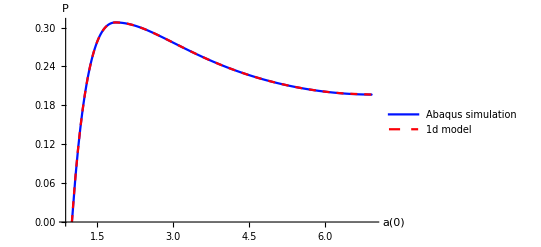

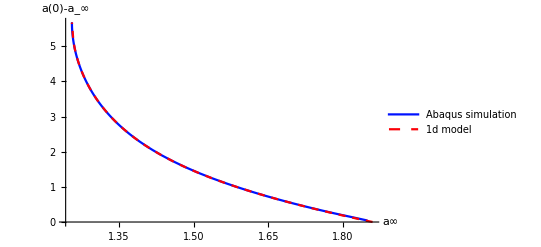

```mathematica
dataPu=Table[{x,Q[x,λN[x]]},{x,1,acr-(acr-1)/nn,(acr-1)/nn}];
dataP1d=Join[dataPu,dataP];
Fig2a=ListPlot[{dataPAbaqus,dataP1d},Joined->True,AxesLabel->{HoldForm[a[0]],HoldForm[P]},LabelStyle->{12,GrayLevel[0]},PlotStyle-> {{RGBColor[0, 0.0691844, 0.99823],Full},{RGBColor[0.985946, 0, 0.0273594],Dashed}},PlotLegends->Placed[LineLegend[{"Abaqus simulation","1d model"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.35}],PlotRange->Full] (* this produces Fig. 2(a) *)
Fig2b=ListPlot[{dataa0Abaqus,dataa0},Joined->True,AxesLabel->{HoldForm[a∞],HoldForm[a[0]-Subscript[a, ∞]]},LabelStyle->{12,GrayLevel[0]},PlotStyle-> {{RGBColor[0, 0.0691844, 0.99823],Full},{RGBColor[0.985946, 0, 0.0273594],Dashed}},PlotLegends->Placed[LineLegend[{"Abaqus simulation","1d model"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.55}]] (* this produces Fig. 2(b)*)
```

### (V). Find the “initial values” for the 1d equation

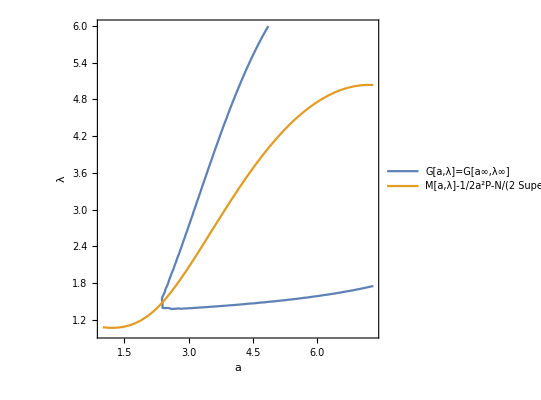

{2.35453,1.45506}

```mathematica
{P1,P2,P3,P4}={0.3,0.25,0.22,0.197};
P=P1;
NN=Nc;
{a∞,λ∞}={x,y}/.FindRoot[{Q[x,y]==P,F[x,y]==Nc},{x,1.5,1,acr},{y,1.01,1,λcr}];
ContourPlot[{G[x,y]==G[a∞,λ∞],eq[x,y]==0},{x,1,7.3},{y,1,6},FrameLabel->{{HoldForm[λ],None},{HoldForm[a],None}},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[LineLegend[{"G[a,λ]=G[a∞,λ∞]","M[a,λ]-1/2a^2P-N/(2 SuperscriptBox[πA, 2])=0"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.25,0.85}]]
a0guess=3; 
λ0guess=2;
{a0,λ0}={x,y}/.FindRoot[ {G[x,y]==G[a∞,λ∞],eq[x,y]==0},{x,a0guess,acr,max},{y,λ0guess,λcr,max}](* this solution should be the intersection point of the two curves in the figure above;  adjust a0guess and λ0guess if necessary*)
```

```mathematica
dataP03Abaqus={{0.,2.354118227958679},{0.1,2.3530516624450684},{0.2,2.349866032600403},{0.30000000000000004,2.3445968627929688},{0.4,2.3373031616210938},{0.5,2.3280651569366455},{0.6000000000000001,2.3169833421707153},{0.7000000000000001,2.304175615310669},{0.8,2.2897756099700928},{0.9,2.2739282846450806},{1.,2.2567896842956543},{1.1,2.2385213375091553},{1.2000000000000002,2.2192893028259277},{1.3,2.1992604732513428},{1.4000000000000001,2.1785991191864014},{1.5,2.157464623451233},{1.6,2.1360247135162354},{1.7000000000000002,2.114421844482422},{1.8,2.0927937030792236},{1.9000000000000001,2.071268320083618},{2.,2.0499625205993652},{2.1,2.02898108959198},{2.2,2.0084176063537598},{2.3000000000000003,1.9883525371551514},{2.4000000000000004,1.9688555002212524},{2.5,1.9499843120574951},{2.6,1.9317858815193176},{2.7,1.9142969846725464},{2.8000000000000003,1.8975445628166199},{2.9000000000000004,1.8815469145774841},{3.,1.866314172744751},{3.1,1.8518494367599487},{3.2,1.8381493091583252},{3.3000000000000003,1.825204849243164},{3.4000000000000004,1.8130024075508118},{3.5,1.8015241026878357},{3.6,1.7907488942146301},{3.7,1.7806529998779297},{3.8000000000000003,1.7712104320526123},{3.9000000000000004,1.7623936533927917},{4.,1.7541742324829102},{4.1000000000000005,1.7465229630470276},{4.2,1.7394103407859802},{4.3,1.732806921005249},{4.4,1.7266836166381836},{4.5,1.7210118174552917},{4.6000000000000005,1.7157636880874634},{4.7,1.71091228723526},{4.800000000000001,1.7064316272735596},{4.9,1.7022969126701355},{5.,1.6984843015670776},{5.1000000000000005,1.6949711441993713},{5.2,1.6917362213134766},{5.300000000000001,1.688759207725525},{5.4,1.686021089553833},{5.5,1.683504045009613},{5.6000000000000005,1.681191325187683},{5.7,1.6790673732757568},{5.800000000000001,1.6771173477172852},{5.9,1.6753279566764832},{6.,1.6736863851547241},{6.1000000000000005,1.6721808910369873},{6.2,1.6708006858825684},{6.300000000000001,1.6695355772972107},{6.4,1.6683763265609741},{6.5,1.6673142910003662},{6.6000000000000005,1.6663415431976318},{6.7,1.6654507517814636},{6.800000000000001,1.6646351218223572},{6.9,1.6638884544372559},{7.,1.6632049083709717},{7.1000000000000005,1.6625794172286987},{7.2,1.6620070338249207},{7.300000000000001,1.661483347415924},{7.4,1.6610041856765747},{7.5,1.6605658531188965},{7.6000000000000005,1.6601648926734924},{7.7,1.6597981452941895},{7.800000000000001,1.6594627499580383},{7.9,1.659156084060669},{8.,1.6588754653930664},{8.1,1.6586190462112427},{8.200000000000001,1.6583844423294067},{8.3,1.6581699848175049},{8.4,1.6579739451408386},{8.5,1.657794713973999},{8.6,1.6576308012008667},{8.700000000000001,1.6574810147285461},{8.8,1.6573440432548523},{8.9,1.6572188138961792},{9.,1.6571044325828552},{9.1,1.6569997668266296},{9.200000000000001,1.6569041013717651},{9.3,1.6568167209625244},{9.4,1.6567368507385254},{9.5,1.656663715839386},{9.600000000000001,1.6565969586372375},{9.700000000000001,1.6565359830856323},{9.8,1.6564801931381226},{9.9,1.65642911195755},{10.,1.6563825011253357}};
```

### (VI). Plot the a[Z]-Z graph by solving the 1d initial value problem

{2023,1,4,22,38,18.2378615}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}

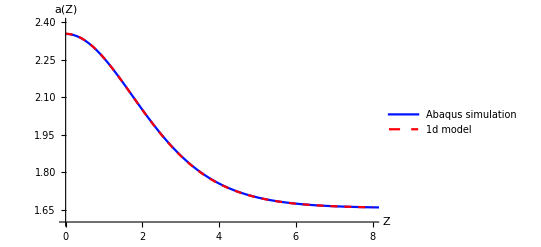

{2023,1,4,22,38,48.9991911}

```mathematica
L=8;
startime=DateList[]
aZsub=NDSolve[{y1'[x]==y2[x],y2'[x]== 1/𝔻[y1[x]](A^2 y1[x] λλ[y1[x]](Q[y1[x],λλ[y1[x]]]-P)-1/2 𝔻p[y1[x]] y2[x]^2),y1[0]==a0,y2[0]==0},{y1,y2},{x,0,L}]//First (*𝔻'[a] is replaced by its numerical approximation, which is significantly faster*)
Fig3=ListPlot[{dataP03Abaqus,Table[{x,y1[x]/.aZsub},{x,0,L,0.01}]},Joined->True,PlotLegends->Placed[LineLegend[{"Abaqus simulation","1d model"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.85}],PlotStyle-> {{RGBColor[0, 0.0691844, 0.99823],Full},{RGBColor[0.985946, 0, 0.0273594],Dashed}},AxesLabel->{HoldForm[Z],HoldForm[a[Z]]},LabelStyle->{12,GrayLevel[0]},PlotRange->{{0,L},{1.6,2.4}}](*this gives Fig. 3*)
endtime=DateList[]
```

## 4. Case 2 : Fixed l = 2 L with L = 20, using the finite difference method

```mathematica
Clear[a,λ,a0,a∞,λ0,λ∞,P,NN,λλ,𝔻,𝔻p,A,B,Rm,H,Δ] (*Clear the variables that needed to be redefined in the finite difference method*)
```

### (I). Re-define the functions λ[a, a∞, λ∞] and D[a, a∞, λ∞] to incorporate the dependence on a∞ and λ∞

```mathematica
λλ[a_?NumericQ,a∞_?NumberQ,λ∞_?NumericQ]:=y/. FindRoot[M[a,y]-1/2 a^2 Q[a∞,λ∞]==F[a∞,λ∞],{y,y0}]
𝔻[a_?NumericQ,a∞_?NumberQ,λ∞_?NumericQ]:=Module[{λz},λz=y/.FindRoot[M[a,y]-1/2 a^2 Q[a∞,λ∞]==F[a∞,λ∞] ,{y,y0}];P=Q[a∞,λ∞];NIntegrate[R ζ[μ,R]((Derivative[1,0][r][μ,R])^2-c[μ,R]^2)/.{λ[μ]->λz, λ'[μ]->λp[a,λz]} /.{μ->a},{R,A,B}]]
Δh=10^-6;
𝔻p[a_?NumericQ,a∞_?NumericQ,λ∞_?NumericQ]:=(𝔻[a+Δh,a∞,λ∞]-𝔻[a-Δh,a∞,λ∞])/(2 Δh)
```

### (II). Geometric parameters

```mathematica
Rm=1;
H=0.4;
A=Rm-H/2
B=Rm+H/2
```

0.8

1.2

### (III). Bifurcation point

```mathematica
λc=2;
acr=x/.FindRoot[Ω[x,λc]==0,{x,1.5}]
Pcr=Q[acr,λc];
bifpt={acr,Pcr}
```

1.73762

{1.73762,0.19831}

### (IV). Define the mesh points and discretize the 1d equation

```mathematica
L=20;
n=40; (*take n=2*L for faster reuslts;one can improve the results by increasing n *)
h=L/n;
ZArray=Array[Z,n+1,0];
aArray=Array[a,n+1,0];
Table[Z[j]=j h,{j,0,n}];
eqs=Table[ A^2 a[j]λλ[a[j],a∞,λ∞](Q[a[j],λλ[a[j],a∞,λ∞]]-Q[a∞,λ∞])-1/2 𝔻p[a[j],a∞,λ∞] ((a[j+1]-a[j-1])/(2h))^2-𝔻[a[j],a∞,λ∞] (a[j-1]-2a[j]+a[j+1])/h^2==0,{j,1,n-1}];
lbc= A^2 a[0]λλ[a[0],a∞,λ∞](Q[a[0],λλ[a[0],a∞,λ∞]]-Q[a∞,λ∞])-2𝔻[a[0],a∞,λ∞] (a[1]-a[0])/h^2==0;
rbc=A^2 a[n]λλ[a[n],a∞,λ∞](Q[a[n],λλ[a[n],a∞,λ∞]]-Q[a∞,λ∞])-1/2 𝔻p[a[n],a∞,λ∞] ω[a∞,λ∞]/𝔻[a∞,a∞,λ∞](a[n]-a∞)^2-2𝔻[a[n],a∞,λ∞] 1/h^2(a[n-1]-a[n]-h √(ω[a∞,λ∞]/𝔻[a∞,a∞,λ∞])(a[n]-a∞))==0;
eqadded=a[0]-a0==0;
Δ=h(1/2 λλ[a[0],a∞,λ∞]+Sum[λλ[a[j],a∞,λ∞],{j,1,n-1}]+1/2 λλ[a[n],a∞,λ∞])-λc L==0;
eqs=Append[eqs,lbc];
eqs=Append[eqs,rbc];
eqs=Append[eqs,eqadded];
eqs=Append[eqs,Δ];
```

### (V). The weakly nonlinear solution with P=0.197, used as the initial guess

```mathematica
a0start=2.068511449204241;
a0=a0start;
ω[a_,λ_]:=(2 a A^2 λ (-Derivative[0,1][Q][a,λ] Derivative[1,0][F][a,λ]+Derivative[0,1][F][a,λ] Derivative[1,0][Q][a,λ]))/(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ]);
γ[a_,λ_]:=1/2 A^2 (2 λ Derivative[1,0][Q][a,λ]+(a (2 Derivative[0,1][Q][a,λ]+λ Derivative[0,2][Q][a,λ]) (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ])^2)/(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ])^2-(2 (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ]) (λ Derivative[0,1][Q][a,λ]+a (Derivative[1,0][Q][a,λ]+λ Derivative[1,1][Q][a,λ])))/(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ])+a λ Derivative[2,0][Q][a,λ]+(a λ Derivative[0,1][Q][a,λ] (-((2 Derivative[0,2][F][a,λ]+a^2 Derivative[0,2][Q][a,λ]) (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ])^2)+2 (2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ]) (2 Derivative[1,0][F][a,λ]+a^2 Derivative[1,0][Q][a,λ]) (2 a Derivative[0,1][Q][a,λ]+2 Derivative[1,1][F][a,λ]+a^2 Derivative[1,1][Q][a,λ])-(2 Derivative[0,1][F][a,λ]+a^2 Derivative[0,1][Q][a,λ])^2 (4 a Derivative[1,0][Q][a,λ]+2 Derivative[2,0][F][a,λ]+a^2 Derivative[2,0][Q][a,λ])))/(8 (Derivative[0,1][F][a,λ]+1/2 a^2 Derivative[0,1][Q][a,λ])^3));
a∞weak=(2 a0 γ[acr,λc]-3 acr Derivative[1,0][ω][acr,λc])/(2 γ[acr,λc]-3 Derivative[1,0][ω][acr,λc]);
yweak[x_]=a∞weak-(3 Derivative[1,0][ω][acr,λc])/(2γ[acr,λc])(a∞weak-acr)Sech[1/2 √((Derivative[1,0][ω][acr,λc])/𝔻[acr,acr,λc](a∞weak-acr))x]^2;
```

### (VI). Find the FD solution

```mathematica
guess=Table[{a[j],yweak[Z[j]]},{j,0,n}];
guess=Append[guess,{a∞,a∞weak}];
guess=Append[guess,{λ∞,λc}]; (*use the weakly nonlinear solution as the initial guess*)
starttime=DateList[]
sub=FindRoot[eqs,guess,MaxIterations->20,WorkingPrecision->6];
endtime=DateList[]
dataP={{a[0],Q[a∞,λ∞]}/.sub};
dataa0={{a[n],a[0]-a[n]}/.sub};
solssub={sub};
(*output the result*)
sub
```

{2023,1,4,23,3,22.1276851}

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (6.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{2023,1,4,23,17,26.7870737}

{a[0]→2.06851,a[1]→2.06458,a[2]→2.05303,a[3]→2.03455,a[4]→2.01022,a[5]→1.98134,a[6]→1.94937,a[7]→1.91572,a[8]→1.88171,a[9]→1.84842,a[10]→1.81673,a[11]→1.78726,a[12]→1.76037,a[13]→1.73625,a[14]→1.71493,a[15]→1.6963,a[16]→1.68021,a[17]→1.66641,a[18]→1.65468,a[19]→1.64476,a[20]→1.63642,a[21]→1.62943,a[22]→1.62361,a[23]→1.61876,a[24]→1.61475,a[25]→1.61142,a[26]→1.60867,a[27]→1.60641,a[28]→1.60455,a[29]→1.60302,a[30]→1.60176,a[31]→1.60074,a[32]→1.59991,a[33]→1.59924,a[34]→1.5987,a[35]→1.59828,a[36]→1.59795,a[37]→1.59771,a[38]→1.59755,a[39]→1.59745,a[40]→1.59742,a∞→1.59579,λ∞→1.95444}

```mathematica
aZAbaqus={{0.,2.066801428794861},{0.1,2.0666438341140747},{0.2,2.066171884536743},{0.30000000000000004,2.0653862953186035},{0.4,2.0642893314361572},{0.5,2.0628833770751953},{0.6000000000000001,2.0611722469329834},{0.7000000000000001,2.0591596364974976},{0.8,2.0568509101867676},{0.9,2.0542513132095337},{1.,2.051363229751587},{1.1,2.0482017993927},{1.2000000000000002,2.0447754859924316},{1.3,2.0410910844802856},{1.4000000000000001,2.037156581878662},{1.5,2.0329809188842773},{1.6,2.028573751449585},{1.7000000000000002,2.023944854736328},{1.8,2.01910400390625},{1.9000000000000001,2.0140621662139893},{2.,2.008829712867737},{2.1,2.0034180879592896},{2.2,1.997838020324707},{2.3000000000000003,1.9921007752418518},{2.4000000000000004,1.9862182140350342},{2.5,1.9802014827728271},{2.6,1.9740619659423828},{2.7,1.9678113460540771},{2.8000000000000003,1.961460828781128},{2.9000000000000004,1.9550219178199768},{3.,1.9485055804252625},{3.1,1.9419228434562683},{3.2,1.9352846145629883},{3.3000000000000003,1.928601324558258},{3.4000000000000004,1.921883463859558},{3.5,1.9151407480239868},{3.6,1.9083834886550903},{3.7,1.9016206860542297},{3.8000000000000003,1.8948615193367004},{3.9000000000000004,1.8881148099899292},{4.,1.8813889026641846},{4.1000000000000005,1.8746918439865112},{4.2,1.8680312037467957},{4.3,1.8614142537117004},{4.4,1.8548478484153748},{4.5,1.8483386039733887},{4.6000000000000005,1.8418921828269958},{4.7,1.8355146646499634},{4.800000000000001,1.8292109370231628},{4.9,1.8229862451553345},{5.,1.8168448209762573},{5.1000000000000005,1.8107908964157104},{5.2,1.8048282861709595},{5.300000000000001,1.7989602088928223},{5.4,1.7931897640228271},{5.5,1.7875196933746338},{5.6000000000000005,1.7819522619247437},{5.7,1.7764896750450134},{5.800000000000001,1.771133542060852},{5.9,1.7658852934837341},{6.,1.7607463002204895},{6.1000000000000005,1.7557172775268555},{6.2,1.7507988214492798},{6.300000000000001,1.7459914684295654},{6.4,1.7412954568862915},{6.5,1.7367106080055237},{6.6000000000000005,1.732236921787262},{6.7,1.727873682975769},{6.800000000000001,1.7236205339431763},{6.9,1.7194766998291016},{7.,1.7154411673545837},{7.1000000000000005,1.7115130424499512},{7.2,1.7076910734176636},{7.300000000000001,1.7039739489555359},{7.4,1.700360357761383},{7.5,1.69684898853302},{7.6000000000000005,1.693437933921814},{7.7,1.6901258826255798},{7.800000000000001,1.6869109272956848},{7.9,1.6837913393974304},{8.,1.6807655692100525},{8.1,1.6778314113616943},{8.200000000000001,1.674987256526947},{8.3,1.6722310781478882},{8.4,1.6695607900619507},{8.5,1.6669747829437256},{8.6,1.664470911026001},{8.700000000000001,1.662047266960144},{8.8,1.6597017645835876},{8.9,1.6574326157569885},{9.,1.655237853527069},{9.1,1.6531153917312622},{9.200000000000001,1.6510634422302246},{9.3,1.649079978466034},{9.4,1.6471632719039917},{9.5,1.6453112959861755},{9.600000000000001,1.6435222625732422},{9.700000000000001,1.6417944431304932},{9.8,1.6401259899139404},{9.9,1.6385149955749512},{10.,1.6369600892066956},{10.100000000000001,1.635459303855896},{10.200000000000001,1.6340110301971436},{10.3,1.6326136589050293},{10.4,1.6312655210494995},{10.5,1.6299653053283691},{10.600000000000001,1.628711223602295},{10.700000000000001,1.627501904964447},{10.8,1.6263359785079956},{10.9,1.6252119541168213},{11.,1.6241283416748047},{11.100000000000001,1.6230839490890503},{11.200000000000001,1.6220775842666626},{11.3,1.6211076378822327},{11.4,1.620173156261444},{11.5,1.6192728877067566},{11.600000000000001,1.6184055805206299},{11.700000000000001,1.6175702810287476},{11.8,1.6167656779289246},{11.9,1.6159908175468445},{12.,1.6152446269989014},{12.100000000000001,1.614526093006134},{12.200000000000001,1.6138343811035156},{12.3,1.6131683588027954},{12.4,1.6125273704528809},{12.5,1.6119104027748108},{12.600000000000001,1.6113163828849792},{12.700000000000001,1.610744833946228},{12.8,1.6101948022842407},{12.9,1.6096655130386353},{13.,1.6091561913490295},{13.100000000000001,1.6086662411689758},{13.200000000000001,1.6081948280334473},{13.3,1.607741355895996},{13.4,1.6073052287101746},{13.5,1.6068856716156006},{13.600000000000001,1.6064821481704712},{13.700000000000001,1.606094241142273},{13.8,1.605721116065979},{13.9,1.605362355709076},{14.,1.6050174236297607},{14.100000000000001,1.60468590259552},{14.200000000000001,1.604367196559906},{14.3,1.6040608286857605},{14.4,1.6037664413452148},{14.5,1.6034835577011108},{14.600000000000001,1.6032116413116455},{14.700000000000001,1.6029505729675293},{14.8,1.6026995778083801},{14.9,1.6024585962295532},{15.,1.60222727060318},{15.100000000000001,1.6020049452781677},{15.200000000000001,1.6017916202545166},{15.3,1.6015867590904236},{15.4,1.6013901829719543},{15.5,1.601201593875885},{15.600000000000001,1.6010205745697021},{15.700000000000001,1.6008469462394714},{15.8,1.6006805300712585},{15.9,1.6005210280418396},{16.,1.6003679633140564},{16.1,1.6002214550971985},{16.2,1.600080966949463},{16.3,1.5999465584754944},{16.400000000000002,1.5998178720474243},{16.5,1.5996947884559631},{16.6,1.599577009677887},{16.7,1.599464476108551},{16.8,1.5993568301200867},{16.900000000000002,1.5992541909217834},{17.,1.599156141281128},{17.1,1.5990626215934753},{17.2,1.5989736318588257},{17.3,1.5988888144493103},{17.400000000000002,1.5988081693649292},{17.5,1.598731517791748},{17.6,1.598658800125122},{17.7,1.5985897779464722},{17.8,1.5985245108604431},{17.900000000000002,1.5984627604484558},{18.,1.5984045267105103},{18.1,1.5983495712280273},{18.2,1.5982980132102966},{18.3,1.5982496738433838},{18.400000000000002,1.5982045531272888},{18.5,1.5981624722480774},{18.6,1.59812331199646},{18.7,1.598087191581726},{18.8,1.5980539321899414},{18.900000000000002,1.598023533821106},{19.,1.5979959964752197},{19.1,1.5979710817337036},{19.200000000000003,1.597948968410492},{19.3,1.5979294776916504},{19.400000000000002,1.5979127287864685},{19.5,1.5978986024856567},{19.6,1.5978869795799255},{19.700000000000003,1.597878098487854},{19.8,1.5978716015815735},{19.900000000000002,1.5978677868843079},{20.,1.5978664755821228}};
```

#### (VII). Compare the FD solution with the Abaqus simulation

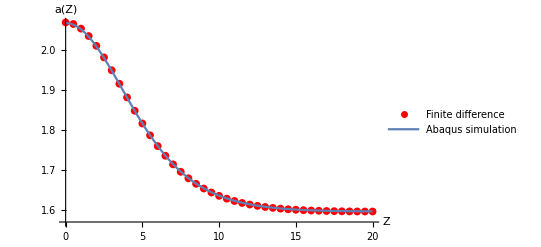

```mathematica
Figfdm=ListPlot[Table[{Z[j],a[j]}/.sub,{j,0,n}],PlotMarkers->{"●",8},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Finite difference"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.75,0.85}]];
FigAbaqus=ListPlot[aZAbaqus,Joined->True,PlotLegends->Placed[LineLegend[{"Abaqus simulation"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.75,0.75}]];
Show[Figfdm,FigAbaqus,AxesLabel->{HoldForm[Z],HoldForm[a[Z]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},Epilog->{Text[Style["P=0.197",12],{10,2.08}]}]
```

### (VIII). Extend the FD Solution to the fully nonlinear regime by numerical continuation, using the result at the previous step as the initial guess for the current step

```mathematica
startime=DateList[]
kmax=5;
Do[a0=a0start-k (a0start-1.03 acr)/kmax;
guess=Table[{a[j],Re[a[j]]/.sub},{j,0,n}];
guess=Append[guess,{a∞,Re[a∞]/.sub}];
guess=Append[guess,{λ∞,Re[λ∞]/.sub}];
sub=FindRoot[eqs,guess,MaxIterations->20,WorkingPrecision->6];
dataP=Prepend[dataP,{a[0],Q[a∞,λ∞]}/.sub];
dataa0=Prepend[dataa0,{a[n],a[0]-a[n]}/.sub];
solssub=Prepend[solssub,sub],{k,1,kmax}]
sub=solssub//Last;
a0end=7.23;
kmax=54;
Do[a0=a0start+k (a0end-a0start)/kmax;
guess=Table[{a[j],Re[a[j]]/.sub},{j,0,n}];
guess=Append[guess,{a∞,Re[a∞]/.sub}];
guess=Append[guess,{λ∞,Re[λ∞]/.sub}];
sub=FindRoot[eqs,guess,MaxIterations->20,WorkingPrecision->6];
dataP=Append[dataP,{a[0],Q[a∞,λ∞]}/.sub];
dataa0=Append[dataa0,{a[n],a[0]-a[n]}/.sub];
solssub=Append[solssub,sub],{k,1,kmax}]
endtime=DateList[]
(*Output the results*)
dataP
dataa0
```

{2023,1,4,23,18,11.767099}

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (6.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (6.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (6.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (6.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in R near {R} = {0.803222319802423}. NIntegrate obtained 0.51738+0.0247628 ⅈ and 0.130209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in R near {R} = {0.803222319802423}. NIntegrate obtained 0.355693+0.220693 ⅈ and 0.110545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in R near {R} = {0.803222319802423}. NIntegrate obtained 0.35942+0.207828 ⅈ and 0.101557 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2023,1,5,9,12,12.34431}

{{1.78975,0.19901},{1.8455,0.198785},{1.90125,0.198428},{1.95701,0.197998},{2.01276,0.197517},{2.06851,0.197002},{2.16409,0.196061},{2.25968,0.195072},{2.35526,0.19405},{2.45084,0.19301},{2.54643,0.191959},{2.64201,0.190904},{2.73759,0.189851},{2.83318,0.188806},{2.92876,0.187772},{3.02434,0.186752},{3.11993,0.185752},{3.21551,0.184772},{3.31109,0.183816},{3.40668,0.182886},{3.50226,0.181985},{3.59784,0.181114},{3.69342,0.180276},{3.78901,0.179471},{3.88459,0.178702},{3.98017,0.17797},{4.07576,0.177277},{4.17134,0.176624},{4.26692,0.176012},{4.36251,0.175444},{4.45809,0.17492},{4.55367,0.174442},{4.64926,0.174012},{4.74484,0.173633},{4.84042,0.173305},{4.93601,0.173032},{5.03159,0.172815},{5.12717,0.172659},{5.22275,0.172567},{5.31834,0.172543},{5.41392,0.172593},{5.5095,0.172723},{5.60509,0.172942},{5.70067,0.17326},{5.79625,0.17369},{5.89184,0.17425},{5.98742,0.174962},{6.083,0.175855},{6.17859,0.176966},{6.27417,0.178337},{6.36975,0.180015},{6.46534,0.182036},{6.56092,0.184417},{6.6565,0.18715},{6.75208,0.190212},{6.84767,0.19358},{6.94325,0.19724},{7.03883,0.201189},{7.13442,0.20542},{7.23+1.98806×10^-20 ⅈ,0.20964+3.56472×10^-6 ⅈ}}

{{1.73959,0.05015},{1.70022,0.1453},{1.66931,0.2319},{1.64295,0.3141},{1.61926,0.3935},{1.59742,0.4711},{1.56311,0.60098},{1.53196,0.72772},{1.5034,0.85187},{1.47711,0.97373},{1.45283,1.0936},{1.43034,1.2117},{1.4095,1.3281},{1.39016,1.443},{1.37217,1.5566},{1.35542,1.6689},{1.33982,1.7801},{1.32527,1.8902},{1.3117,1.9994},{1.29903,2.1076},{1.2872,2.2151},{1.27615,2.3217},{1.26582,2.4276},{1.25618,2.5328},{1.24717,2.6374},{1.23877,2.7414},{1.23093,2.8448},{1.22362,2.9477},{1.21682,3.0501},{1.21049,3.152},{1.20462,3.2535},{1.19918,3.3545},{1.19416,3.4551},{1.18954,3.5553},{1.1853,3.6551},{1.18142,3.7546},{1.17791,3.8537},{1.17475,3.9524},{1.17194,4.0508},{1.16947,4.1489},{1.16735,4.2466},{1.16557,4.3439},{1.16416,4.4409},{1.16314,4.5375},{1.16253,4.6337},{1.1624,4.7294},{1.16284,4.8246},{1.16399,4.919},{1.16605,5.0125},{1.16933,5.1048},{1.17424,5.1955},{1.18127,5.2841},{1.19088,5.37},{1.2034,5.4531},{1.21896,5.5331},{1.23746,5.6102},{1.2587,5.6845},{1.28237,5.7565},{1.30768,5.8267},{1.32564+0.0000142895 ⅈ,5.9044-0.0000142895 ⅈ}}

```mathematica
dataPAbaqus={{0.707080066204071,0.},{0.7547620981931686,0.03429973125457764},{0.8154271245002747,0.0685377836227417},{0.875043623149395,0.09451936483383179},{0.9337847754359245,0.11460444927215577},{0.9917868347838521,0.13038015365600586},{1.0491581782698631,0.14294358491897582},{1.1059866547584534,0.15307304859161378},{1.1623443514108658,0.1613318681716919},{1.218291088938713,0.1681350111961365},{1.2738771736621857,0.17379294633865358},{1.3291454017162323,0.17854111194610597},{1.3841327726840973,0.1825602173805237},{1.4388720095157623,0.18599048852920533},{1.4933931231498718,0.18894182443618776},{1.5477259159088135,0.19150112867355348},{1.6019051671028137,0.1937376618385315},{1.6559882760047913,0.19570710659027102},{1.7101629972457886,0.19745434522628785},{1.765213668346405,0.19888617992401125},{1.7945228815078735,0.19895838499069216},{1.822720229625702,0.19887218475341797},{1.853235900402069,0.19872273206710817},{1.8863646388053894,0.19851804971694947},{1.9221612811088562,0.19826184511184694},{1.9605976939201355,0.1979569435119629},{2.0016034841537476,0.19760595560073854},{2.04508376121521,0.19721139669418336},{2.090928554534912,0.1967757821083069},{2.1390169858932495,0.19630172252655032},{2.1892207860946655,0.19579187631607056},{2.2414053678512573,0.1952490210533142},{2.2954317331314087,0.19467608928680422},{2.3511565923690796,0.1940760612487793},{2.408434271812439,0.19345206022262573},{2.4671173095703125,0.19280723333358765},{2.5270577669143677,0.19214481115341187},{2.5881083011627197,0.1914680004119873},{2.6501230001449585,0.19077999591827394},{2.7129589319229126,0.19008392095565796},{2.7764768600463867,0.18938285112380981},{2.8405420780181885,0.1886796832084656},{2.905025005340576,0.18797720670700074},{2.969802141189575,0.18727803230285645},{3.0347561836242676,0.18658461570739748},{3.09977650642395,0.18589917421340943},{3.1647589206695557,0.18522377014160157},{3.2296066284179688,0.18456023931503296},{3.29422926902771,0.18391023874282839},{3.3585431575775146,0.1832751989364624},{3.422471284866333,0.18265637159347536},{3.485942840576172,0.18205484151840212},{3.5488932132720947,0.18147149085998537},{3.6112635135650635,0.18090708255767823},{3.6730005741119385,0.1803621768951416},{3.734056234359741,0.17983723878860475},{3.794387102127075,0.17933256626129152},{3.853955030441284,0.1788483738899231},{3.9127256870269775,0.17838476896286012},{3.9706690311431885,0.17794172763824465},{4.027759313583374,0.17751917839050294},{4.083973407745361,0.17711697816848757},{4.139292478561401,0.17673487663269044},{4.193700551986694,0.17637261152267458},{4.24718451499939,0.17602984905242922},{4.299733638763428,0.17570621967315675},{4.3513405323028564,0.17540131807327272},{4.401999235153198,0.17511470317840577},{4.451706409454346,0.17484591007232667},{4.500460863113403,0.1745944619178772},{4.548263311386108,0.17435986995697023},{4.595115423202515,0.17414162158966065},{4.641021490097046,0.17393920421600342},{4.685986280441284,0.17375210523605347},{4.730016708374023,0.17357980012893678},{4.773120164871216,0.17342177629470826},{4.815305471420288,0.17327752113342287},{4.8565826416015625,0.1731465220451355},{4.896962404251099,0.17302829027175903},{4.936455726623535,0.1729223132133484},{4.9750752449035645,0.17282812595367433},{5.012833595275879,0.17274526357650757},{5.049744129180908,0.172673237323761},{5.085821151733398,0.1726116180419922},{5.121078014373779,0.17255996465682985},{5.155529975891113,0.17251785993576052},{5.189191818237305,0.17248489856719973},{5.222078800201416,0.17246066331863405},{5.254205703735352,0.17244479656219483},{5.28558874130249,0.17243691682815554},{5.316540718078613,0.17243671417236328},{5.346475124359131,0.17244384288787842},{5.3757123947143555,0.1724579453468323},{5.404268264770508,0.17247868776321412},{5.43215799331665,0.17250579595565796},{5.459397792816162,0.17253897190093995},{5.4860029220581055,0.17257792949676515},{5.511988162994385,0.1726224184036255},{5.537369728088379,0.17267218828201295},{5.562161922454834,0.1727270007133484},{5.5863800048828125,0.1727866291999817},{5.610039234161377,0.1728508472442627},{5.633152961730957,0.17291946411132814},{5.655736446380615,0.1729922652244568},{5.677803993225098,0.17306908369064333},{5.699368953704834,0.17314972877502444},{5.720445156097412,0.17323403358459474},{5.741045951843262,0.1733218550682068},{5.7611846923828125,0.17341302633285524},{5.780874252319336,0.17350741624832156},{5.8001275062561035,0.17360488176345826},{5.8189568519592285,0.17370530366897585},{5.837374687194824,0.17380856275558473},{5.8553924560546875,0.17391453981399538},{5.873022556304932,0.17402312755584717},{5.890275478363037,0.1741342306137085},{5.907163143157959,0.17424775362014772},{5.923696517944336,0.1743636131286621},{5.939886093139648,0.17448172569274903},{5.955742359161377,0.17460200786590577},{5.971275806427002,0.17472437620162964},{5.986495494842529,0.17484878301620485},{6.001412391662598,0.17497515678405762},{6.016035079956055,0.17510343790054322},{6.0303730964660645,0.1752335786819458},{6.044435501098633,0.17536550760269165},{6.058230876922607,0.1754991888999939},{6.071768283843994,0.1756345868110657},{6.085055828094482,0.17577164173126222},{6.098101615905762,0.1759103298187256},{6.1109137535095215,0.17605061531066896},{6.123499393463135,0.17619245052337648},{6.135867118835449,0.1763358235359192},{6.14802360534668,0.1764807105064392},{6.159976005554199,0.17662706375122073},{6.171730995178223,0.1767748832702637},{6.183296203613281,0.1769241452217102},{6.194677829742432,0.1770748257637024},{6.2058820724487305,0.1772269129753113},{6.216915607452393,0.17738039493560792},{6.227784156799316,0.17753525972366335},{6.238493919372559,0.1776914954185486},{6.249050617218018,0.17784909009933472},{6.259459495544434,0.17800804376602175},{6.269726276397705,0.17816834449768068},{6.2798566818237305,0.17833000421524048},{6.289855003356934,0.17849299907684327},{6.299727439880371,0.17865734100341799},{6.309477806091309,0.1788230299949646},{6.319111347198486,0.17899006605148315},{6.328632831573486,0.1791584610939026},{6.338047027587891,0.17932820320129395},{6.347357273101807,0.1794993042945862},{6.356568813323975,0.17967177629470826},{6.36568546295166,0.17984561920166017},{6.374711513519287,0.18002083301544192},{6.383650779724121,0.18019745349884034},{6.3925065994262695,0.18037546873092652},{6.4012837409973145,0.18055490255355836},{6.409985065460205,0.1807357668876648},{6.418613910675049,0.18091806173324587},{6.4271745681762695,0.18110181093215943},{6.435669898986816,0.18128702640533448},{6.444103717803955,0.1814737319946289},{6.452478408813477,0.18166192770004275},{6.460797309875488,0.18185164928436282},{6.469063758850098,0.18204290866851808},{6.477280616760254,0.18223572969436647},{6.485450267791748,0.18243011236190798},{6.493576526641846,0.1826261043548584},{6.50166130065918,0.1828237056732178},{6.509707450866699,0.18302295207977295},{6.5177178382873535,0.18322386741638186},{6.525694847106934,0.1834264636039734},{6.5336408615112305,0.18363077640533448},{6.541558742523193,0.183836829662323},{6.549449920654297,0.1840446472167969},{6.557317733764648,0.18425425291061404},{6.565164089202881,0.18446569442749025},{6.572990894317627,0.18467897176742554},{6.580800533294678,0.18489413261413576},{6.588595390319824,0.18511121273040773},{6.596376895904541,0.1853302359580994},{6.604147911071777,0.1855512261390686},{6.611909866333008,0.18577423095703127},{6.619665145874023,0.18599928617477418},{6.627415180206299,0.1862264156341553},{6.635161876678467,0.18645566701889038},{6.642907619476318,0.18668707609176638},{6.65065336227417,0.18692066669464114},{6.6584014892578125,0.18715649843215942},{6.666153907775879,0.18739460706710817},{6.673912048339844,0.1876350283622742},{6.681677341461182,0.1878778100013733},{6.689451694488525,0.18812298774719238},{6.697237014770508,0.18837062120437623},{6.7050347328186035,0.18862075805664064},{6.712845802307129,0.18887342214584352},{6.720673084259033,0.1891286849975586},{6.728517055511475,0.18938659429550173},{6.736379623413086,0.18964719772338867},{6.744262218475342,0.18991055488586428},{6.752166271209717,0.19017670154571534},{6.760093688964844,0.19044572114944458},{6.768045425415039,0.19071764945983888},{6.7760233879089355,0.19099255800247195},{6.78402853012085,0.1912704944610596},{6.792062759399414,0.1915515422821045},{6.800127029418945,0.19183573722839356},{6.808222770690918,0.1921231746673584},{6.816351890563965,0.19241390228271485},{6.824515342712402,0.19270799160003663},{6.832714557647705,0.19300551414489747},{6.840950965881348,0.19330655336380007},{6.849225997924805,0.19361118078231812},{6.857541084289551,0.19391945600509644},{6.865897178649902,0.19423147439956667},{6.874295711517334,0.1945473074913025},{6.88273811340332,0.19486703872680666},{6.891225814819336,0.19519076347351075},{6.899759769439697,0.1955185651779175},{6.908341884613037,0.1958505153656006},{6.916973114013672,0.19618672132492065},{6.925654411315918,0.19652727842330933},{6.93438720703125,0.1968722701072693},{6.943173408508301,0.19722180366516115},{6.9520134925842285,0.19757596254348755},{6.960908889770508,0.19793486595153809},{6.969861030578613,0.1982986092567444},{6.978870868682861,0.19866731166839602},{6.987939357757568,0.19904105663299562},{6.997067928314209,0.19941996335983278},{7.006258010864258,0.19980413913726808},{7.015510082244873,0.20019369125366213},{7.024825572967529,0.20058875083923342},{7.034205436706543,0.2009894371032715},{7.043649673461914,0.2013958215713501},{7.053160667419434,0.2018080472946167},{7.062737941741943,0.20222623348236085},{7.07238245010376,0.20265047550201418},{7.082094669342041,0.2030808925628662},{7.0918755531311035,0.20351755619049072},{7.101724147796631,0.20396060943603517},{7.1116414070129395,0.20441014766693116},{7.121626853942871,0.20486621856689455},{7.131679534912109,0.20532889366149903},{7.141798973083496,0.20579824447631836},{7.151983261108398,0.20627431869506838},{7.162230968475342,0.20675711631774904},{7.172538757324219,0.20724656581878664},{7.182903289794922,0.20774264335632325},{7.193319320678711,0.20824520587921144},{7.2037811279296875,0.20875401496887208},{7.214279651641846,0.20926878452301026},{7.224803447723389,0.20978899002075196},{7.22901725769043,0.2099984645843506}};
dataa0Abaqus={{1.7423843741416931,0.05213850736618042},{1.7255576848983765,0.09716254472732544},{1.707506239414215,0.145729660987854},{1.6888579726219177,0.19750666618347168},{1.6699485778808594,0.2522127032279968},{1.650979459285736,0.3096182346343994},{1.6320742964744568,0.36952918767929077},{1.6133129000663757,0.43177086114883423},{1.5947523713111877,0.49617618322372437},{1.5764392614364624,0.5625777244567871},{1.5584152936935425,0.630805492401123},{1.5407203435897827,0.7006850242614746},{1.5233926177024841,0.7720391154289246},{1.5064681768417358,0.8446884155273438},{1.4899804592132568,0.9184538125991821},{1.4739591181278229,0.9931581914424896},{1.458429753780365,1.0686280131340027},{1.443413257598877,1.1446950435638428},{1.4289257228374481,1.2211972773075104},{1.414978414773941,1.2979805171489716},{1.4015780687332153,1.3748987913131714},{1.3887270092964172,1.4518150687217712},{1.3764236867427826,1.5286013185977936},{1.3646630346775055,1.6051391065120697},{1.353437066078186,1.6813191175460815},{1.3427351415157318,1.7570413649082184},{1.3325445652008057,1.83221435546875},{1.3228510022163391,1.9067556262016296},{1.3136387765407562,1.9805904924869537},{1.3048913180828094,2.053651839494705},{1.296591341495514,2.125879943370819},{1.2887212336063385,2.1972216069698334},{1.2812631726264954,2.2676300406455994},{1.2741993963718414,2.337064117193222},{1.2675122916698456,2.405488282442093},{1.2611844837665558,2.4728717505931854},{1.2551990151405334,2.5391880869865417},{1.2495394498109818,2.6044155806303024},{1.244189739227295,2.6685359477996826},{1.2391344755887985,2.73153455555439},{1.234358787536621,2.793400526046753},{1.229848399758339,2.8541250079870224},{1.2255896478891373,2.913702830672264},{1.221569448709488,2.9721311032772064},{1.2177753299474716,3.029409185051918},{1.2141953855752945,3.0855382531881332},{1.2108182907104492,3.1405222415924072},{1.2076332420110703,3.194365993142128},{1.2046300172805786,3.247076392173767},{1.2017988562583923,3.298662006855011},{1.1991305649280548,3.3491327464580536},{1.1966163665056229,3.398499056696892},{1.1942479759454727,3.446773514151573},{1.1920174956321716,3.4939687848091125},{1.1899175196886063,3.540099188685417},{1.1879409849643707,3.585179179906845},{1.1860812157392502,3.629224255681038},{1.1843319088220596,3.672250732779503},{1.1826871037483215,3.714275300502777},{1.1811411529779434,3.7553145736455917},{1.179688736796379,3.7953865081071854},{1.178324818611145,3.834508776664734},{1.1770446449518204,3.872699484229088},{1.1758437156677246,3.909977436065674},{1.1747177988290787,3.9463602155447006},{1.1736629158258438,3.9818670600652695},{1.1726752668619156,4.016516551375389},{1.171751320362091,4.050327479839325},{1.1708876937627792,4.083318009972572},{1.1700812578201294,4.115507483482361},{1.1693218797445297,4.147218838334084},{1.1686215251684189,4.177853599190712},{1.167969897389412,4.2077424973249435},{1.1673645228147507,4.236903741955757},{1.1668030470609665,4.265354946255684},{1.166283294558525,4.293114498257637},{1.1658031940460205,4.320199728012085},{1.1653607785701752,4.34662738442421},{1.1649542599916458,4.372415468096733},{1.164581909775734,4.3975800126791},{1.1642421185970306,4.422137886285782},{1.1639333814382553,4.446105852723122},{1.1636542826890945,4.4694986790418625},{1.1634035110473633,4.492332935333252},{1.1631798148155212,4.514624178409576},{1.1629820317029953,4.536386922001839},{1.1628090888261795,4.557636067271233},{1.1626599580049515,4.57838599383831},{1.162533700466156,4.5986509919166565},{1.1624294221401215,4.6184448301792145},{1.1623463034629822,4.637781202793121},{1.1622835844755173,4.656673267483711},{1.1622405499219894,4.675134137272835},{1.1622165143489838,4.693175941705704},{1.1622108817100525,4.710811674594879},{1.162223070859909,4.728052407503128},{1.1622525453567505,4.7449105978012085},{1.1622988134622574,4.7613977044820786},{1.1623614430427551,4.777524650096893},{1.162439987063408,4.793302372097969},{1.1625340729951859,4.808741733431816},{1.1626433581113815,4.823852136731148},{1.1627674847841263,4.838644906878471},{1.1629061996936798,4.853128880262375},{1.1630592048168182,4.867313891649246},{1.1632262617349625,4.88120923936367},{1.1634071469306946,4.894823729991913},{1.163601666688919,4.908166617155075},{1.1638096421957016,4.921246185898781},{1.1640309244394302,4.9340706914663315},{1.1642653495073318,4.94664840400219},{1.1645127981901169,4.958986595273018},{1.1647731810808182,4.971093937754631},{1.1650464087724686,4.982977196574211},{1.165332391858101,4.994643613696098},{1.1656310707330704,5.006099924445152},{1.1659424155950546,5.017353788018227},{1.1662663668394089,5.028411462903023},{1.166602909564972,5.0392791628837585},{1.1669520437717438,5.049963563680649},{1.1673137545585632,5.060470402240753},{1.1676880568265915,5.070805862545967},{1.168074980378151,5.080975636839867},{1.1684745252132416,5.090984970331192},{1.168886736035347,5.100839540362358},{1.1693116873502731,5.110544994473457},{1.1697493940591812,5.120105609297752},{1.1701999455690384,5.129527494311333},{1.1706633865833282,5.13881441950798},{1.171139806509018,5.147971540689468},{1.1716292947530746,5.157003536820412},{1.1721319258213043,5.165915101766586},{1.1726477891206741,5.1747094839811325},{1.1731770038604736,5.183391809463501},{1.1737196743488312,5.191965788602829},{1.174275889992714,5.200435623526573},{1.1748457998037338,5.208804979920387},{1.1754295080900192,5.21707709133625},{1.1760271340608597,5.225256606936455},{1.1766388416290283,5.233346223831177},{1.1772647500038147,5.241349160671234},{1.1779049932956696,5.2492695748806},{1.1785597503185272,5.257110148668289},{1.1792291402816772,5.264874577522278},{1.179913341999054,5.272565066814423},{1.1806125044822693,5.280184805393219},{1.1813268065452576,5.28773695230484},{1.182056412100792,5.295224204659462},{1.1828014850616455,5.3026487827301025},{1.183562234044075,5.310014292597771},{1.1843388229608536,5.317322477698326},{1.1851314306259155,5.324576020240784},{1.1859402805566788,5.331777557730675},{1.1867655515670776,5.338929295539856},{1.1876074373722076,5.346033424139023},{1.1884661614894867,5.353092581033707},{1.1893419176340103,5.360108003020287},{1.1902349442243576,5.367082789540291},{1.1911454498767853,5.374018639326096},{1.19207364320755,5.380917251110077},{1.1930197775363922,5.3877807557582855},{1.1939840614795685,5.394611328840256},{1.1949667632579803,5.401410132646561},{1.1959680914878845,5.408179819583893},{1.1969883292913437,5.414921537041664},{1.1980277001857758,5.421637445688248},{1.1990864723920822,5.428328707814217},{1.2001649141311646,5.434996962547302},{1.201263278722763,5.441644340753555},{1.2023818641901016,5.448271498084068},{1.2035209089517593,5.454880580306053},{1.2046807259321213,5.461473181843758},{1.2058615982532501,5.468050450086594},{1.2070638239383698,5.474613517522812},{1.2082876861095428,5.4811640083789825},{1.2095334976911545,5.487703517079353},{1.2108015716075897,5.494233161211014},{1.2120922207832336,5.500753581523895},{1.2134057730436325,5.507267311215401},{1.2147425413131714,5.513774514198303},{1.216102883219719,5.520276740193367},{1.2174871265888214,5.52677509188652},{1.2188956141471863,5.5332706570625305},{1.2203287035226822,5.539764985442162},{1.221786767244339,5.5462586581707},{1.2232701480388641,5.552753239870071},{1.2247792184352875,5.559249311685562},{1.2263143807649612,5.565748378634453},{1.2278760075569153,5.57225102186203},{1.2294644862413406,5.578758284449577},{1.2310802191495895,5.585271671414375},{1.2327236235141754,5.591791719198227},{1.2343951016664505,5.598319455981255},{1.2360950708389282,5.604855895042419},{1.2378239780664444,5.61140201985836},{1.2395822256803513,5.6179588586091995},{1.2413702756166458,5.6245269030332565},{1.2431885749101639,5.63110713660717},{1.2450375705957413,5.637700542807579},{1.2469177097082138,5.644308105111122},{1.2488294839859009,5.650930285453796},{1.2507733702659607,5.657568514347076},{1.2527498006820679,5.664223313331604},{1.254759281873703,5.670895129442215},{1.2568023204803467,5.677584886550903},{1.258879393339157,5.684294015169144},{1.2609909772872925,5.691022515296936},{1.263137549161911,5.697771340608597},{1.265319675207138,5.704541355371475},{1.267537772655487,5.711333096027374},{1.269792377948761,5.718146979808807},{1.2720839381217957,5.724983990192413},{1.2744129598140717,5.731845051050186},{1.2767798900604248,5.738730192184448},{1.2791852056980133,5.745640367269516},{1.2816292941570282,5.752576142549515},{1.2841126024723053,5.759537070989609},{1.2866354882717133,5.76652517914772},{1.2891983091831207,5.773539632558823},{1.2918013036251068,5.780581146478653},{1.294444739818573,5.787649929523468},{1.2971287369728088,5.794746816158295},{1.2998533844947815,5.801870763301849},{1.3026186227798462,5.809022784233093},{1.3054242432117462,5.816202610731125},{1.3082699179649353,5.823409616947174},{1.3111550211906433,5.830643951892853},{1.3140787780284882,5.83790448307991},{1.3170399963855743,5.8451909720897675},{1.3200371265411377,5.852501630783081},{1.3230681121349335,5.859835177659988},{1.3261303007602692,5.867189019918442},{1.3292202353477478,5.87456089258194},{1.3323334455490112,5.8819462060928345},{1.3354641497135162,5.889339298009872},{1.3367197215557098,5.89229753613472}};
```

#### (IX). Plot the P-a0 and (a0-a∞)-a∞ curves

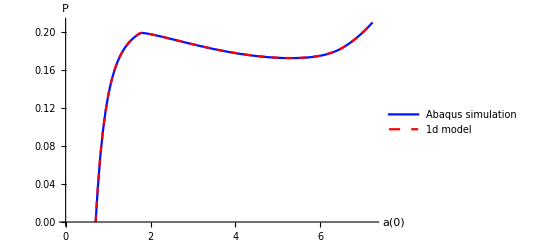

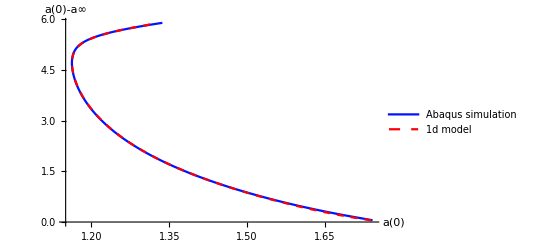

```mathematica
amin=x/.FindRoot[Q[x,λc]==0,{x,0.8}];
dataPu=Table[{x,Q[x,λc]},{x,amin,acr,(acr-amin)/200}];
dataP1d=Join[dataPu,Re[dataP]];
dataa01d=Re[dataa0];
Fig4a=ListPlot[{dataPAbaqus,dataP1d},Joined->True,AxesLabel->{HoldForm[a[0]],HoldForm[P]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotStyle-> {{RGBColor[0, 0.0691844, 0.99823],Full},{RGBColor[0.985946, 0, 0.0273594],Dashed}},PlotLegends->Placed[LineLegend[{"Abaqus simulation","1d model"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.45}]] (*this produces Fig. 4(a)*)
Fig4b=ListPlot[{dataa0Abaqus,dataa01d},Joined->True,AxesLabel->{HoldForm[a[0]],HoldForm[a[0]-a∞]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotStyle-> {{RGBColor[0, 0.0691844, 0.99823],Full},{RGBColor[0.985946, 0, 0.0273594],Dashed}},PlotLegends->Placed[LineLegend[{"Abaqus simulation","1d model"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.45}],PlotRange->Full] (*this produces Fig. 4(b)*)
```